```mathematica
filename = "/usr/local/google/home/aizatsky/projects/iflam/build/render.h5";
```

```mathematica
d = Import[filename, {"Datasets", "d"}];
r = Import[filename, {"Datasets", "r"}];
g = Import[filename, {"Datasets", "g"}];
```

```mathematica
b = Import[filename, {"Datasets", "b"}];
```

```mathematica
annotations =  Flatten[Import[filename, {"Annotations"}]]
```

{iterations→{10000000},samples→{7797559},width→{300},height→{300},filename→/usr/local/google/home/aizatsky/projects/iflam/flam-java/flams/e_6.flam3e}

```mathematica
{Dimensions[d],
Dimensions[r],
Dimensions[g],
Dimensions[b]}
```

{{300,300},{300,300},{300,300},{300,300}}

```mathematica
img = MapThread[Thread[{#1, #2, #3, #4}]&, {r, g, b, d}];
```

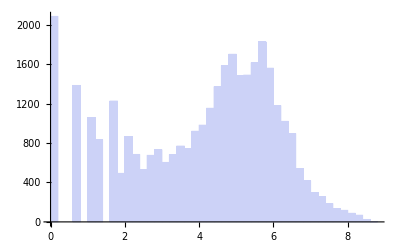

```mathematica
Histogram[Log[Flatten[d]]]
```

```mathematica
RenderPixel[r_, g_, b_, d_,k1_, k2_, gamma_]:=If[d == 0, {0, 0, 0}, 
Module[
{ls = k1 * Log[1 + d * k2]/d},
{(r * ls)^gamma,(g * ls)^gamma, (b *ls)^gamma}]];
```

```mathematica
RenderImage[img_, k1_, k2_, gamma_]:= Map[
RenderPixel[#[[1]], #[[2]], #[[3]], #[[4]], k1, k2, gamma]&, 
img, {2}];
```

```mathematica
RenderImage[img, 1.5]; // AbsoluteTiming
```

{0.01005,Null}

```mathematica
Manipulate[Image[RenderImage[img, k1, k2, gamma]], {{k1, 1}, 0, 2}, {{k2, .01}, 0, 0.1}, {{gamma, 1.26}, 0, 5}]
```

```mathematica
Image[img]
```

-Graphics-